

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
2/3
```

2/3

```mathematica
2/6
```

1/3

```mathematica
Manipulate[
Plot[Normalize[{x,x^3}].Normalize[{x,a}],{x,-3,3},PlotRange->{-5,5}]
,{a,-5,5}]
```

```mathematica
Manipulate[
Plot[
{a,Normalize[{x,x^3}].Normalize[{x,a}]}
,{x,-3,3},PlotRange->{-5,5}]
,{a,-5,5}]
```

```mathematica
With[{f=Function[x,x^3]},
Manipulate[
Plot[
{a,f[x],Normalize[{x,f[x]}].Normalize[{x,a}]}
,{x,-3,3}
,PlotRange->{-5,5}
]
,{a,-5,5}
]
]
```

```mathematica
With[{f=Function[x,x^3]},
Manipulate[
Plot[
{a,f[x],{x,f[x]}.{x,a}}
,{x,-3,3}
,PlotRange->{-5,5}
]
,{a,-5,5}
]
]
```

```mathematica
With[{f=Function[x,x^3]},
Manipulate[
Plot[
{a,f[x],Normalize[{x,f[x]}].Normalize[{x,a}]}
,{x,-3,3}
,PlotRange->{-5,5}
]
,{a,-5,5}
]
]
```

```mathematica
With[{f=Function[x,x^3]},
Manipulate[
Plot3D[
{a,f[x],Normalize[{x,f[x]}].Normalize[{x,a}]}
,{x,-3,3}
,PlotRange->{-5,5}
]
,{a,-5,5}
]
]
```

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

```mathematica
FullSimplify[Abs[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}],x∈Reals]
```

{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}

```mathematica
FullSimplify[{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}/(Total@{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}),x∈Reals]
```

{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}

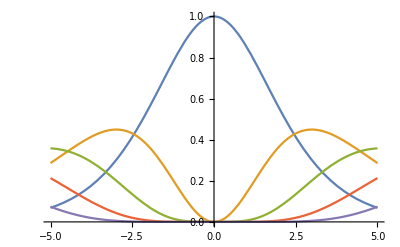

```mathematica
Plot[
{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-5,5}]
```

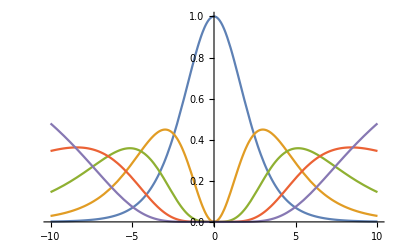

```mathematica
Plot[
{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-10,10}]
```

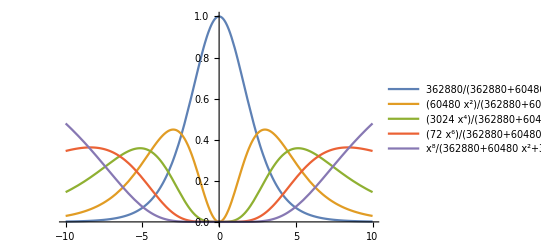

```mathematica
Plot[
{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}
,{x,-10,10},PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[
Total@{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}==1
,{x,-5,5}]
```

FullSimplify::bass: -5 is not a well-formed assumption.

FullSimplify::bass: 5 is not a well-formed assumption.

True

```mathematica
Map[Function[x,#]&,{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}

```mathematica
FullSimplify[
Map[(#''[x])/((√(1+(#'[x])^2))^3)&,{Function[x,x],Function[x,-x^3/6],Function[x,x^5/120],Function[x,-x^7/5040],Function[x,x^9/362880]}]
,x∈Reals]
```

{0,-(8 x)/((4+x^4)^(3/2)),(2304 x^3)/((576+x^8)^(3/2)),-(3110400 x^5)/((518400+x^12)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))}

```mathematica
FullSimplify[Abs[{0,-(8 x)/((4+x^4)^(3/2)),(2304 x^3)/((576+x^8)^(3/2)),-(3110400 x^5)/((518400+x^12)^(3/2)),x^7/(5040 (1+x^16/1625702400)^(3/2))}],x∈Reals]
```

{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))}

```mathematica
FullSimplify[{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))}/(Total@{0,(8 Abs[x])/((4+x^4)^(3/2)),(2304 Abs[x]^3)/((576+x^8)^(3/2)),(3110400 Abs[x]^5)/((518400+x^12)^(3/2)),Abs[x]^7/(5040 (1+x^16/1625702400)^(3/2))}),x∈Reals]
```

{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}

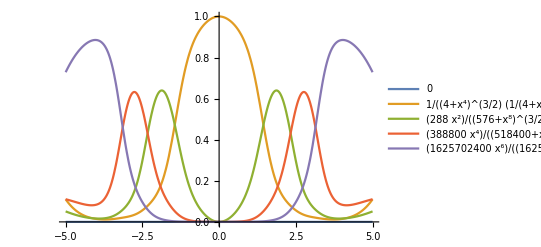

```mathematica
Plot[
{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}
,{x,-5,5},PlotRange->Full,PlotLegends->"Expressions"]
```

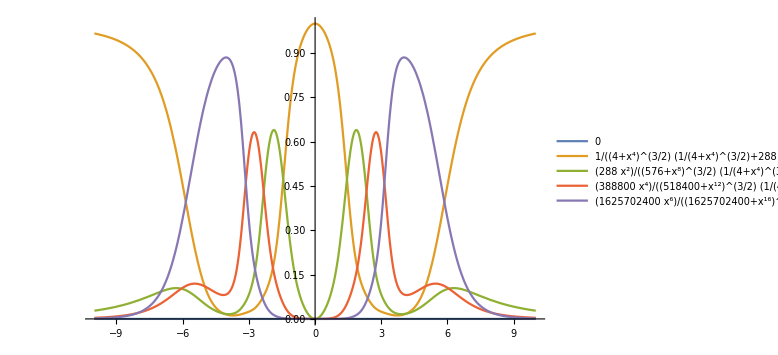

```mathematica
Plot[
{0,1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}
,{x,-10,10}
,PlotRange->Full,PlotLegends->"Expressions",ImageSize->Large]
```

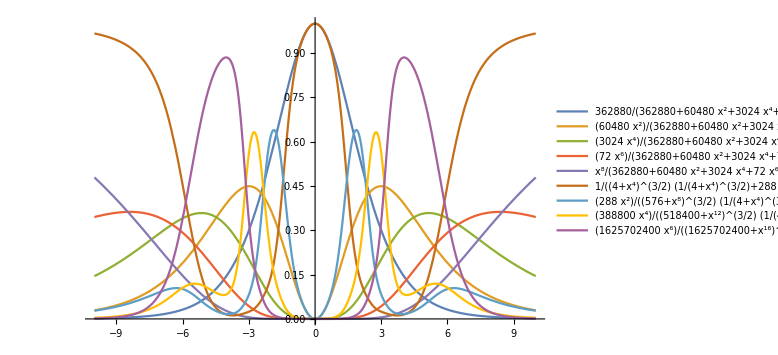

```mathematica
Plot[
{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8),1/((4+x^4)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(288 x^2)/((576+x^8)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(388800 x^4)/((518400+x^12)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2))))),(1625702400 x^6)/((1625702400+x^16)^(3/2) (1/((4+x^4)^(3/2))+288 x^2 (1/((576+x^8)^(3/2))+(1350 x^2)/((518400+x^12)^(3/2))+(5644800 x^4)/((1625702400+x^16)^(3/2)))))}
,{x,-10,10}
,PlotRange->Full,PlotLegends->"Expressions",ImageSize->Large]
```

```mathematica
appl=FinancialData["NASDAQ:AAPL","Price",All]
```

TimeSeries[…]

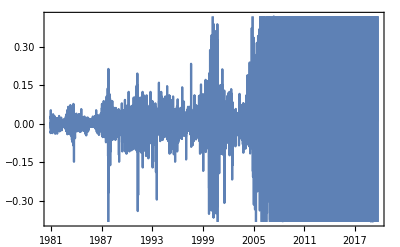

```mathematica
DateListPlot[
Transpose[{
appl["Dates"][[;;-2]],
Differences@appl["Values"]
}]]
```

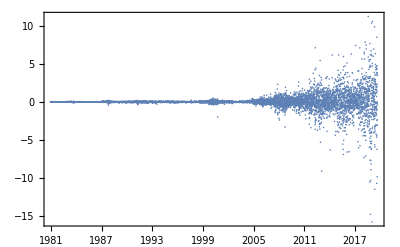

```mathematica
DateListPlot[
Transpose[{
appl["Dates"][[;;-2]],
Differences@appl["Values"]
}],PlotRange->Full,ImageSize->Full,Joined->False,ColorFunction->"DarkRainbow"]
```

```mathematica
TakeLargestBy[
Transpose[{
appl["Dates"][[;;-2]],
Differences@appl["Values"]
}]
,Last,10]
```

{{Tue 31 Jul 2018 00:00:00GMT-7.,11.21 $},{Tue 29 Jan 2019 00:00:00GMT-7.,10.57 $},{Mon 24 Dec 2018 00:00:00GMT-7.,10.34 $},{Tue 30 Apr 2019 00:00:00GMT-7.,9.85 $},{Mon 12 Aug 2019 00:00:00GMT-7.,8.49 $},{Fri 23 Mar 2018 00:00:00GMT-7.,7.83 $},{Thu 11 Oct 2018 00:00:00GMT-7.,7.66 $},{Tue 1 May 2018 00:00:00GMT-7.,7.47 $},{Tue 31 Jan 2017 00:00:00GMT-7.,7.40 $},{Tue 24 Apr 2012 00:00:00GMT-7.,7.10 $}}

```mathematica
aps=Transpose[{
appl["Dates"][[;;-2]],
Differences@appl["Values"]
}];
```

```mathematica
TakeLargestBy[aps,Last,10]
```

{{Tue 31 Jul 2018 00:00:00GMT-7.,11.21 $},{Tue 29 Jan 2019 00:00:00GMT-7.,10.57 $},{Mon 24 Dec 2018 00:00:00GMT-7.,10.34 $},{Tue 30 Apr 2019 00:00:00GMT-7.,9.85 $},{Mon 12 Aug 2019 00:00:00GMT-7.,8.49 $},{Fri 23 Mar 2018 00:00:00GMT-7.,7.83 $},{Thu 11 Oct 2018 00:00:00GMT-7.,7.66 $},{Tue 1 May 2018 00:00:00GMT-7.,7.47 $},{Tue 31 Jan 2017 00:00:00GMT-7.,7.40 $},{Tue 24 Apr 2012 00:00:00GMT-7.,7.10 $}}

```mathematica
Grid@
TakeLargestBy[aps,Last,10]
```

Tue 31 Jul 2018 00:00:00GMT-7. | 11.21 $
Tue 29 Jan 2019 00:00:00GMT-7. | 10.57 $
Mon 24 Dec 2018 00:00:00GMT-7. | 10.34 $
Tue 30 Apr 2019 00:00:00GMT-7. | 9.85 $
Mon 12 Aug 2019 00:00:00GMT-7. | 8.49 $
Fri 23 Mar 2018 00:00:00GMT-7. | 7.83 $
Thu 11 Oct 2018 00:00:00GMT-7. | 7.66 $
Tue 1 May 2018 00:00:00GMT-7. | 7.47 $
Tue 31 Jan 2017 00:00:00GMT-7. | 7.40 $
Tue 24 Apr 2012 00:00:00GMT-7. | 7.10 $

```mathematica
Grid[TakeSmallestBy[aps,Last,10]]
```

Wed 2 Jan 2019 00:00:00GMT-7. | -15.73 $
Thu 1 Nov 2018 00:00:00GMT-7. | -14.74 $
Fri 10 May 2019 00:00:00GMT-7. | -11.46 $
Fri 2 Aug 2019 00:00:00GMT-7. | -10.68 $
Tue 9 Oct 2018 00:00:00GMT-7. | -10.51 $
Fri 9 Nov 2018 00:00:00GMT-7. | -10.30 $
Thu 22 Aug 2019 00:00:00GMT-7. | -9.82 $
Wed 23 Jan 2013 00:00:00GMT-7. | -9.07 $
Mon 19 Nov 2018 00:00:00GMT-7. | -8.88 $
Mon 3 Dec 2018 00:00:00GMT-7. | -8.13 $

```mathematica
Grid[TakeSmallestBy[aps,Last,10]]
```

Wed 2 Jan 2019 00:00:00GMT-7. | -15.73 $
Thu 1 Nov 2018 00:00:00GMT-7. | -14.74 $
Fri 10 May 2019 00:00:00GMT-7. | -11.46 $
Fri 2 Aug 2019 00:00:00GMT-7. | -10.68 $
Tue 9 Oct 2018 00:00:00GMT-7. | -10.51 $
Fri 9 Nov 2018 00:00:00GMT-7. | -10.30 $
Thu 22 Aug 2019 00:00:00GMT-7. | -9.82 $
Wed 23 Jan 2013 00:00:00GMT-7. | -9.07 $
Mon 19 Nov 2018 00:00:00GMT-7. | -8.88 $
Mon 3 Dec 2018 00:00:00GMT-7. | -8.13 $

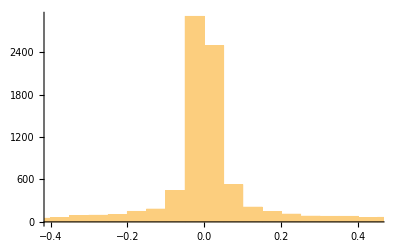

```mathematica
Histogram[Differences@appl["Values"]]
```

```mathematica
Total@Differences@appl["Values"]
```

208.68 $

```mathematica
FinancialData["NASDAQ:AAPL","Price"]
```

209.19 $

```mathematica
TakeLargestBy[aps,First,10]
```

{{Tue 3 Sep 2019 00:00:00GMT-7.,3.49 $},{Fri 30 Aug 2019 00:00:00GMT-7.,-3.04 $},{Thu 29 Aug 2019 00:00:00GMT-7.,-0.27 $},{Wed 28 Aug 2019 00:00:00GMT-7.,3.48 $},{Tue 27 Aug 2019 00:00:00GMT-7.,1.37 $},{Mon 26 Aug 2019 00:00:00GMT-7.,-2.33 $},{Fri 23 Aug 2019 00:00:00GMT-7.,3.85 $},{Thu 22 Aug 2019 00:00:00GMT-7.,-9.82 $},{Wed 21 Aug 2019 00:00:00GMT-7.,-0.18 $},{Tue 20 Aug 2019 00:00:00GMT-7.,2.28 $}}

```mathematica
Grid@TakeLargestBy[aps,First,10]
```

Tue 3 Sep 2019 00:00:00GMT-7. | 3.49 $
Fri 30 Aug 2019 00:00:00GMT-7. | -3.04 $
Thu 29 Aug 2019 00:00:00GMT-7. | -0.27 $
Wed 28 Aug 2019 00:00:00GMT-7. | 3.48 $
Tue 27 Aug 2019 00:00:00GMT-7. | 1.37 $
Mon 26 Aug 2019 00:00:00GMT-7. | -2.33 $
Fri 23 Aug 2019 00:00:00GMT-7. | 3.85 $
Thu 22 Aug 2019 00:00:00GMT-7. | -9.82 $
Wed 21 Aug 2019 00:00:00GMT-7. | -0.18 $
Tue 20 Aug 2019 00:00:00GMT-7. | 2.28 $

```mathematica
Manipulate[
a
,{a,0,∞}]
```

```mathematica
Manipulate[
a
,{a,-∞,∞}]
```

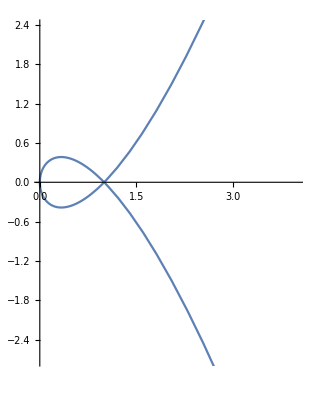

```mathematica
ParametricPlot[
{t^2,t(t^2-1)}
,{t,-2,2}]
```

```mathematica
Solve[{t^2==1,t(t^2-1)==0},t]
```

{{t→-1},{t→1}}

```mathematica
FullSimplify[Norm@D[{t^2,t(t^2-1)},t],t∈Reals]
```

√(1-2 t^2+9 t^4)

```mathematica
Integrate[√(1-2 t^2+9 t^4),{t,-1,1}]
```

∫_-1^1 √(1-2 t^2+9 t^4)ⅆt

```mathematica
NIntegrate[√(1-2 t^2+9 t^4),{t,-1,1}]
```

2.71559

```mathematica
Integrate[√(x'[t]^2+y'[t]^2),{t,a,b}]==Integrate[√(x'[t]^2+y'[t]^2),{t,b,a}]
```

∫_a^b √(x'[t]^2+y'[t]^2)ⅆt==∫_b^a √(x'[t]^2+y'[t]^2)ⅆt

```mathematica
FullSimplify[Integrate[√(x'[t]^2+y'[t]^2),{t,a,b}]==Integrate[√(x'[t]^2+y'[t]^2),{t,b,a}],{t,a,b}∈Reals]
```

∫_a^b √(x'[t]^2+y'[t]^2)ⅆt==∫_b^a √(x'[t]^2+y'[t]^2)ⅆt

```mathematica
r==p q
```

r==p q

```mathematica
r==p [q]q
```

r==q p[q]

```mathematica
r[q]==p [q]q
```

r[q]==q p[q]

```mathematica
Dt[r[q]==p [q]q]
```

Dt[q] r'[q]==Dt[q] p[q]+q Dt[q] p'[q]

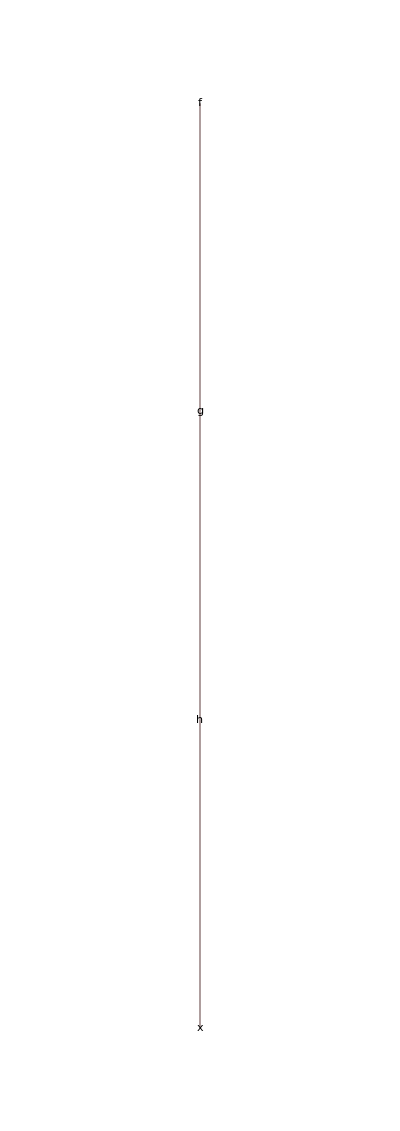

```mathematica
TreeForm@f[g[h[x]]]
```

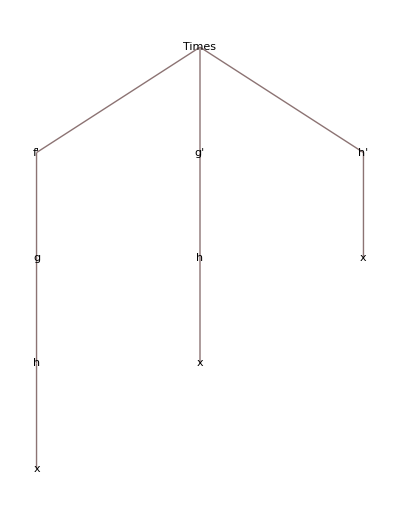

```mathematica
TreeForm@D[f[g[h[x]]],x]
```

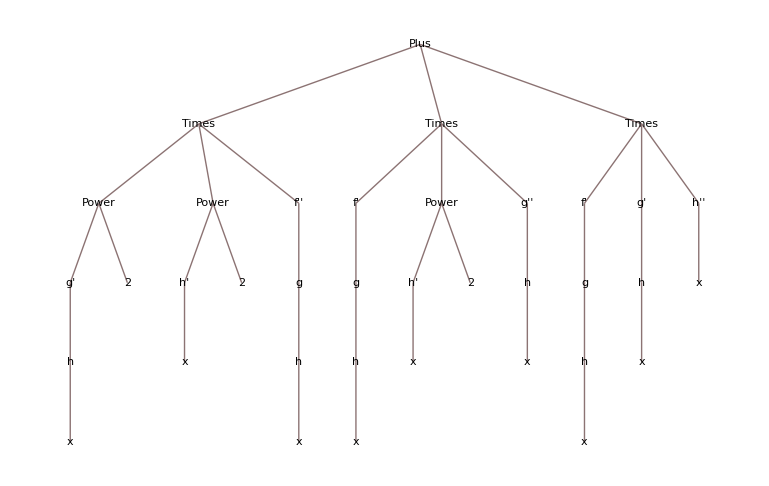

```mathematica
TreeForm@D[f[g[h[x]]],{x,2}]
```

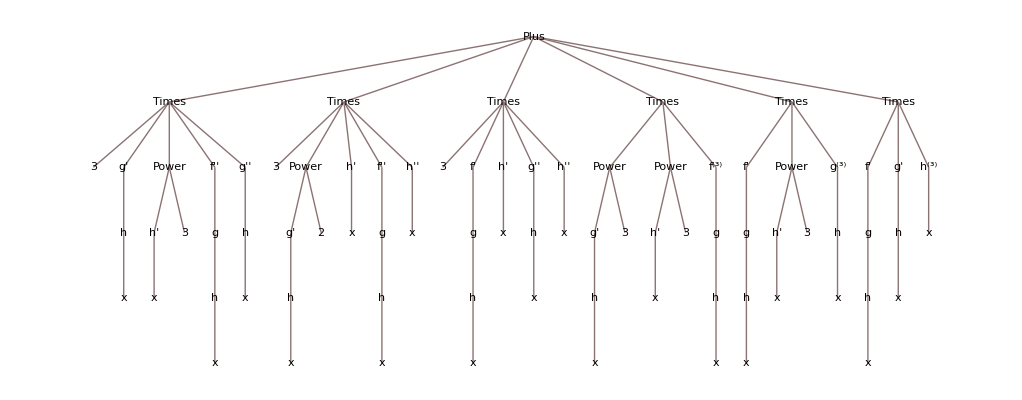

```mathematica
TreeForm@D[f[g[h[x]]],{x,3}]
```

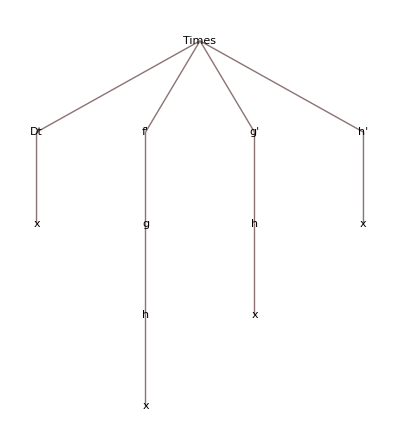

```mathematica
TreeForm@Dt[f[g[h[x]]]]
```

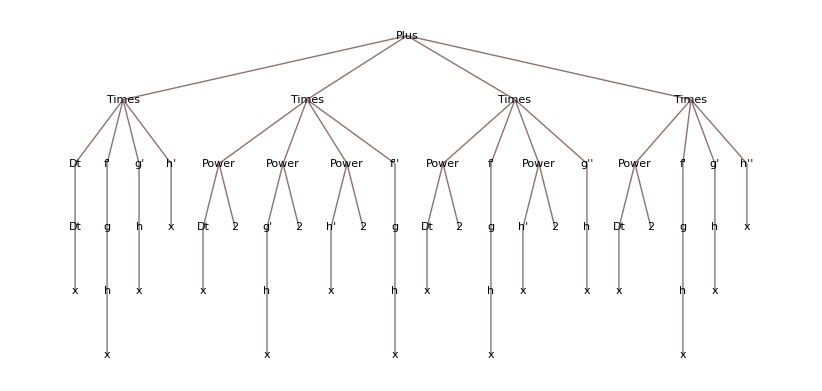

```mathematica
TreeForm@Dt@Dt[f[g[h[x]]]]
```

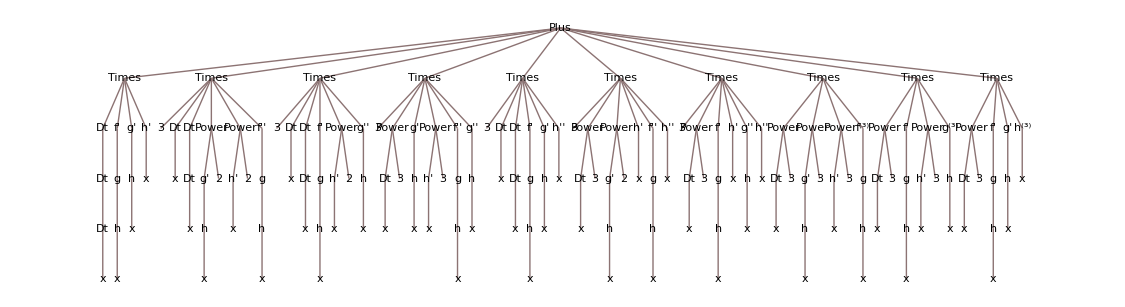

```mathematica
TreeForm@Dt@Dt@Dt[f[g[h[x]]]]
```

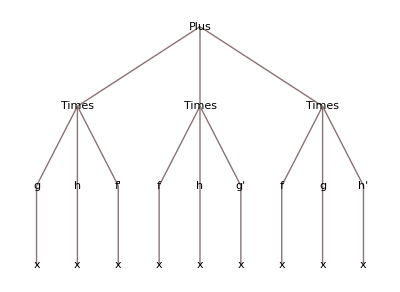

```mathematica
TreeForm@D[f[x]g[x]h[x],{x,1}]
```

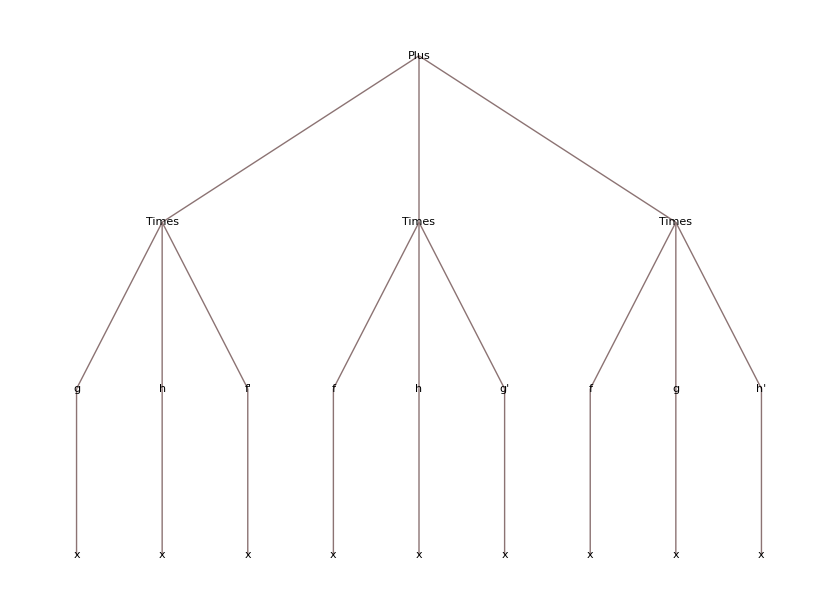
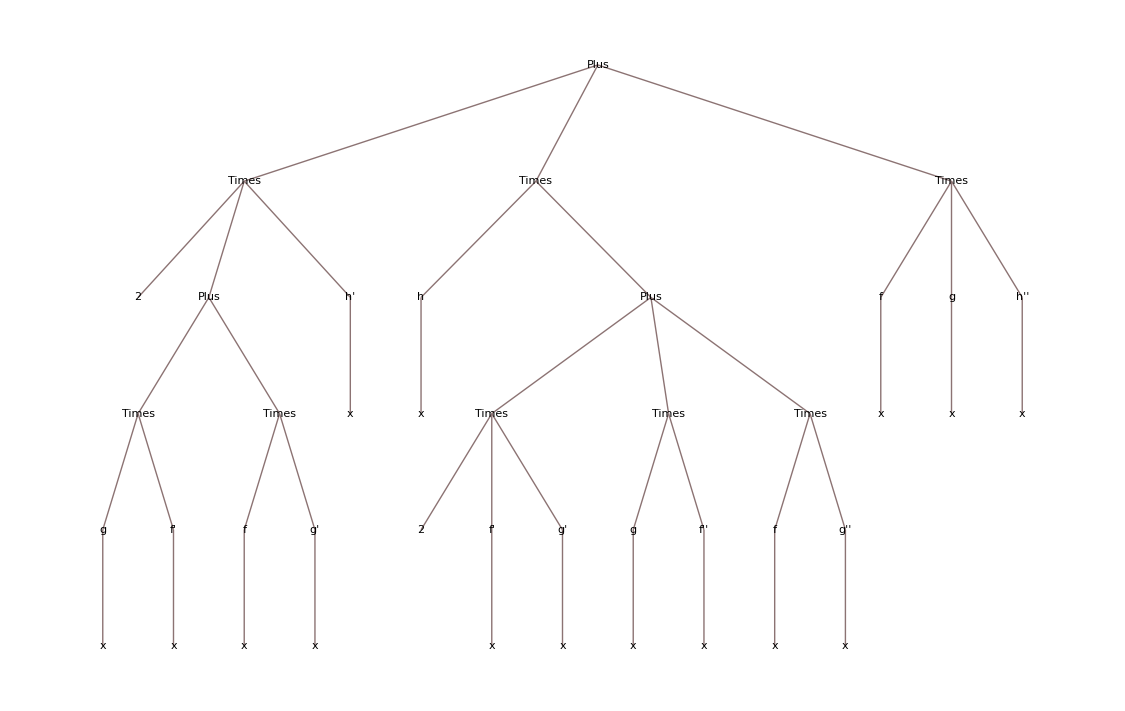
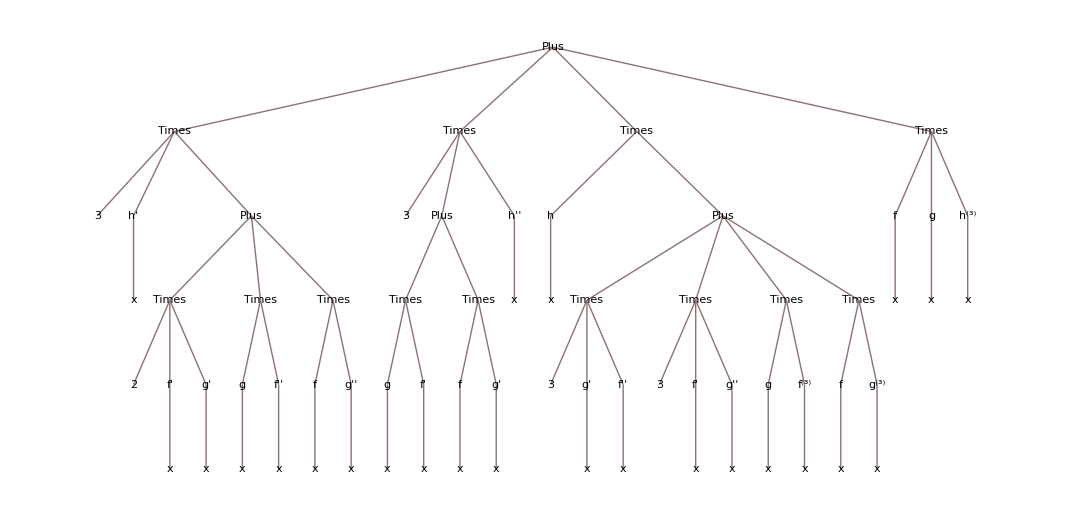

```mathematica
Table[TreeForm@D[f[x]g[x]h[x],{x,i}],{i,1,3}]
```

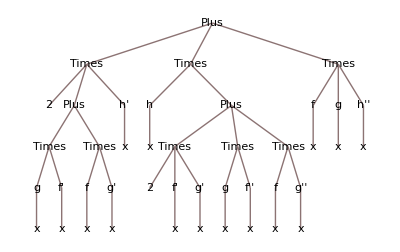
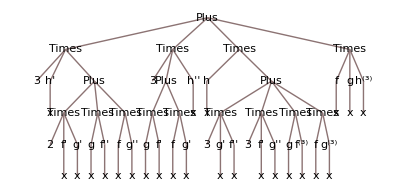
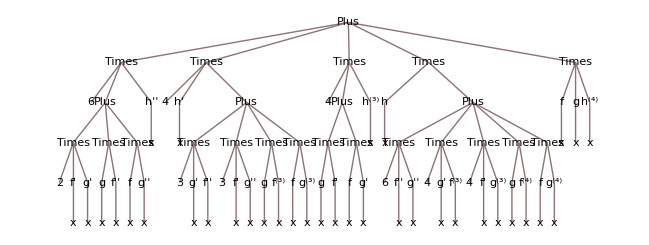
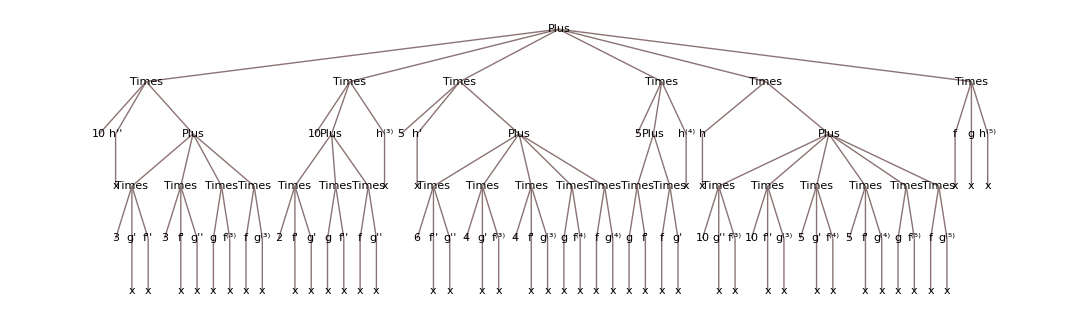
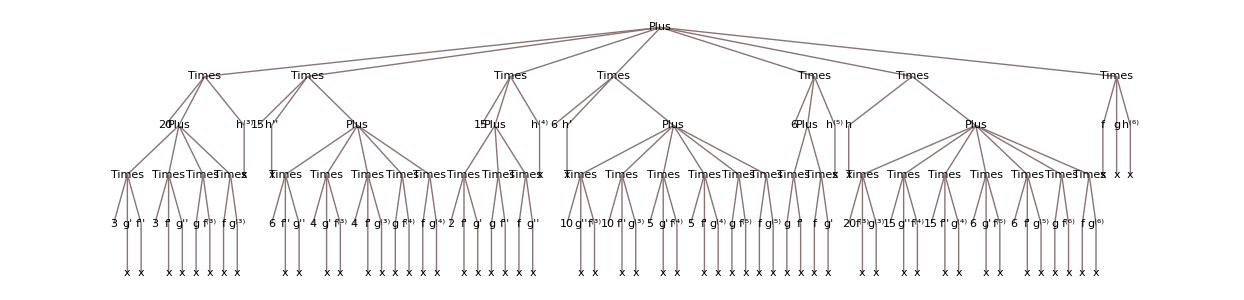
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[TreeForm@D[f[x]g[x]h[x],{x,i}],{i,1,6}]
```

```mathematica
x^n+y^n==z^n
```

x^n+y^n==z^n

```mathematica
FindInstance[x^n+y^n==z^n,{n,x,y,z}]
```

$Aborted

```mathematica
x^n+y^n==z^n/.n->2
```

x^2+y^2==z^2

```mathematica
FindInstance[x^2+y^2==z^2,{x,y,z}]
```

{{x→0,y→0,z→0}}

```mathematica
FindInstance[x^2+y^2==z^2,{x,y,z},2]
```

{{x→3/5-10 ⅈ,y→-14/5-(53 ⅈ)/10,z→-1/10 √(-11989+1768 ⅈ)},{x→16/5+(17 ⅈ)/5,y→-41/5-(43 ⅈ)/5,z→1/5 √(-201+4070 ⅈ)}}

```mathematica
FindInstance[x^2+y^2==z^2,{x,y,z},2,]
```

FindInstance::intpm: Positive machine-sized integer expected at position 4 in FindInstance.

FindInstance[x^2+y^2==z^2,{x,y,z},2,]

```mathematica
FindInstance[x^2+y^2==z^2,{x,y,z},,2]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[x^2+y^2==z^2,{x,y,z},,2]

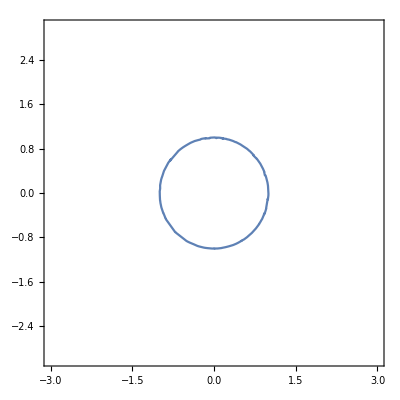

```mathematica
ContourPlot[x^2+y^2-1==0,{x,y}∈Disk[{0,0},3]]
```